## Active polymer driven by correlated excitations

This notebook illustrates the effects of correlated excitations (that is, we deal with a non-diagonal correlation function) on the polymer conformation, and shows how these excitations elicit effective long-ranged interactions. For the correlation function, we choose a box function.

Load required packages.

```mathematica
Once@AppendTo[$Path,NotebookDirectory[]<>"Source/Dense/"];
Needs["KernelGeneric`"->None,"KernelGeneric.wl"];
```

Specialize the loaded kernels.

```mathematica
(* position correlation between different points *)
PositionCorrelationActivity[s1_,s2_]=FullSimplify[KernelGeneric`CorrelationActivity[s1,s2,0],Assumptions->{s1>0,s2>0}]/.{s1->Abs[s1],s2->Abs[s2]};
(* tangent correlation between different points *)
TangentCorrelationActivity[s1_,s2_]=FullSimplify[KernelGeneric`CorrelationActivity[s1,s2,1]/.{HeavisideTheta[-s1]->1-HeavisideTheta[s1],HeavisideTheta[-s2]->1-HeavisideTheta[s2]}];
(* effective interactions between different points *)
StiffnessActivity[s1_,s2_]=FullSimplify@Collect[FullSimplify[KernelGeneric`StiffnessActivity[s1,s2]/.{HeavisideTheta[-s1]->1-HeavisideTheta[s1],HeavisideTheta[-s2]->1-HeavisideTheta[s2]}],{DiracDelta[s2] DiracDelta''[s1],DiracDelta[s1] DiracDelta''[s2]}];
```

Helper function that integrates the kernels over a box.

```mathematica
BoxIntegrate[fun_,s1_,s2_]:=Module[{step},
step[1]=fun[s1-s1i,s2-s2i];
step[2]=Integrate[step[1],s1i]//FullSimplify;
step[3]=FullSimplify[(step[2]/.s1i->1/2)-(step[2]/.s1i->-1/2)];
step[4]=Integrate[step[3],s2i];
step[5]=FullSimplify[(step[4]/.s2i->1/2)-(step[4]/.s2i->-1/2)];
Return[step[5]];
];
```

Determine functions that we will later plot: “position” is the position correlation function in response to a box-shaped correlation function; “shape” is the tangent autocorrelation function; “interaction” encodes the effective harmonic interactions.

```mathematica
fun[s1_,s2_]=FullSimplify[StiffnessActivity[s1,s2],{s1>0,s2>0}];
interaction[s1_,s2_]=BoxIntegrate[fun,s1,s2]//FullSimplify;

fun[s1_,s2_]=FullSimplify[PositionCorrelationActivity[s1,s2],{s1>0,s2>0}];
(position[s1_,s2_]:=Limit[#,{x1->s1,x2->s2}])&@FullSimplify@BoxIntegrate[fun,x1,x2];

fun[s1_,s2_]=FullSimplify[TangentCorrelationActivity[s1,s2],{s1>0,s2>0}];
(shape[s1_,s2_]:=Limit[#,{x1->s1,x2->s2}])&@FullSimplify@BoxIntegrate[fun,x1,x2];
```

Plot effective interactions between different points.

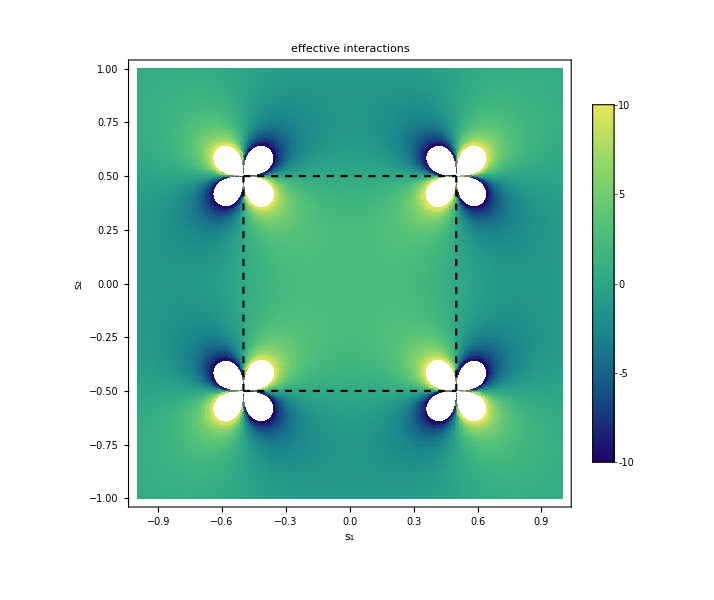

```mathematica
interactionrange=10;
colorlist=ColorData["BlueGreenYellow"]/@Table[x,{x,0,1,1/255}];

Show[
{DensityPlot[
interaction[x,y],
{x,-1,1},{y,-1,1},
ColorFunctionScaling->False,
ColorFunction->(Blend[colorlist,Rescale[#,{-interactionrange,interactionrange}]]&),
ImageSize->600,
Background->None,
PlotRange->{{-1,1},{-1,1},{-interactionrange,interactionrange}},
PlotPoints->100,
PlotLegends->Automatic,
PlotLabel->"effective interactions",
FrameLabel->{Subscript[s, 1],Subscript[s, 2]}
],
ParametricPlot[{{1/2,x},{-1/2,x},{x,-1/2},{x,1/2}},{x,-1/2,1/2},PlotStyle->Directive[Dashed,Thick,Black]]}
]
```

Plot tangent correlation between different points.

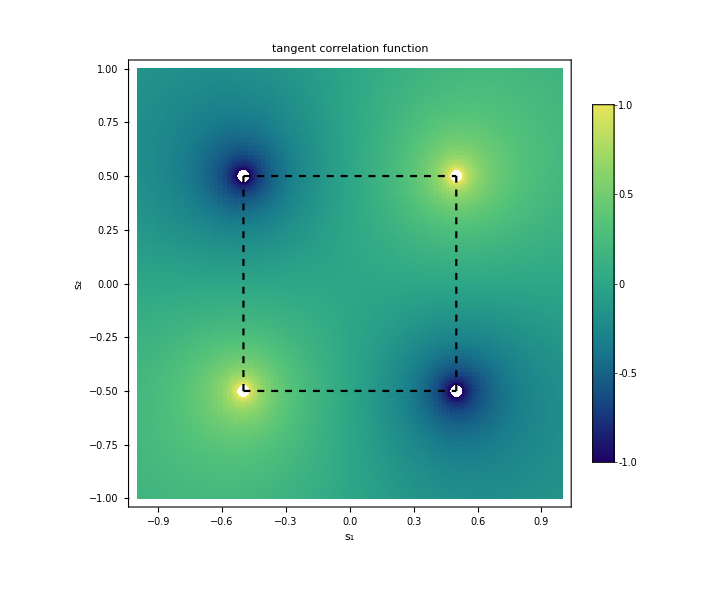

```mathematica
ttrange=1;
colorlist=ColorData["BlueGreenYellow"]/@Table[x,{x,0,1,1/255}];

Show[
{DensityPlot[
shape[x,y],
{x,-1,1},{y,-1,1},
ColorFunctionScaling->False,
ColorFunction->(Blend[colorlist,Rescale[#,{-ttrange,ttrange}]]&),
ImageSize->600,
Background->None,
PlotRange->{{-1,1},{-1,1},{-ttrange,ttrange}},
PlotPoints->100,
PlotLegends->Automatic,
PlotLabel->"tangent correlation function",
FrameLabel->{Subscript[s, 1],Subscript[s, 2]}
],
ParametricPlot[{{1/2,x},{-1/2,x},{x,-1/2},{x,1/2}},{x,-1/2,1/2},PlotStyle->Directive[Dashed,Thick,Black]]}
]
```

Plot position correlation between different points.

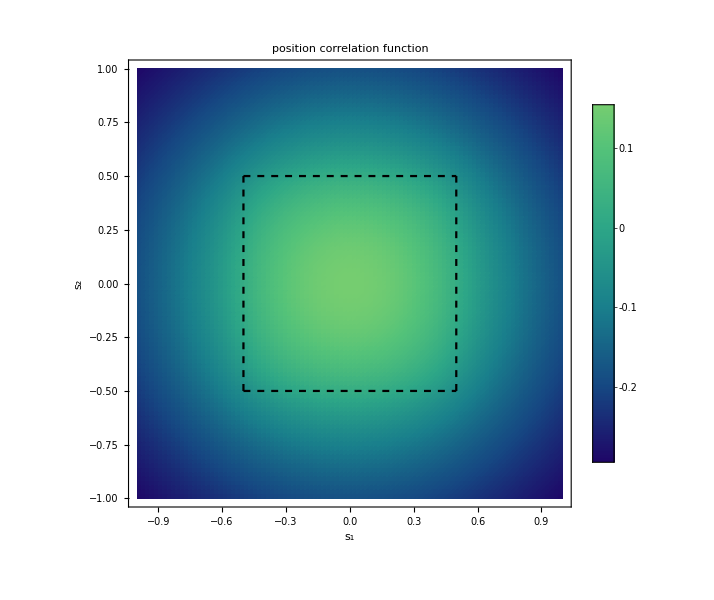

```mathematica
separationrange=0.3;
colorlist=ColorData["BlueGreenYellow"]/@Table[x,{x,0,1,1/255}];

Show[
{DensityPlot[
position[x,y],
{x,-1,1},{y,-1,1},
ColorFunctionScaling->False,
ColorFunction->(Blend[colorlist,Rescale[#,{-separationrange,separationrange}]]&),
ImageSize->600,
Background->None,
PlotRange->{{-1,1},{-1,1},{-separationrange,separationrange}},
PlotPoints->100,
PlotLegends->Automatic,
PlotLabel->"position correlation function",
FrameLabel->{Subscript[s, 1],Subscript[s, 2]}
],
ParametricPlot[{{1/2,x},{-1/2,x},{x,-1/2},{x,1/2}},{x,-1/2,1/2},PlotStyle->Directive[Dashed,Thick,Black]]}
]
```